NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in egamma near {egamma} = {0.000126559}. NIntegrate obtained 3.26525×10^28 and 2.99594×10^24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in egamma near {egamma} = {0.0000607414}. NIntegrate obtained 2.05983×10^28 and 5.02585×10^24 for the integral and error estimates.

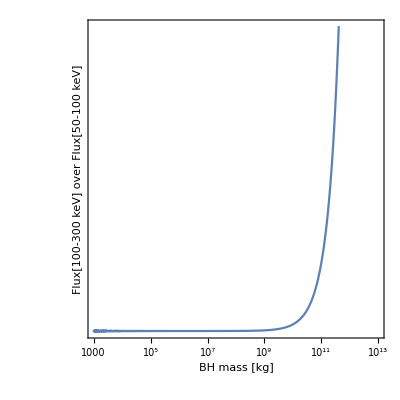

```mathematica
x[egamma_,MBH_]:=egamma/(1.058(10^10/MBH));

(* parameterization in Eq. (31-34) of 1510/.04372 *)
Aparam=6.339 10^23;
Bparam=1.1367 10^24;
ThetaS[u_]:=0.5*(1.+Tanh[10.*u]);

d2NdEdtfrag[egamma_,MBH_]:=Aparam*x[egamma,MBH ]*(1-ThetaS[x[egamma,MBH ]-0.3])+Bparam*Exp[-x[egamma,MBH ]]*ThetaS[x[egamma,MBH ]-0.3]/(x[egamma,MBH ]*(x[egamma,MBH ]+1));

Ffunc[y_]:=If[y<2,1.,Exp[-0.0962-1.982(Log[y]-1.908)*(1.+Tanh[20.*(Log[y]-1.908)])]]


d2NdEdtdirect[egamma_,MBH_]:=(1.13 10^19 (x[egamma,MBH ])^6)/(Exp[x[egamma,MBH ]]-1.)*Ffunc[x[egamma,MBH ]]

(*MBHl=10^5;
LogLogPlot[{d2NdEdtfrag[eg,MBHl],d2NdEdtdirect[eg,MBHl]},{eg,1,10^6}]*)

PhotonFlux[MBH_,Elow_,Ehigh_]:=NIntegrate[d2NdEdtfrag[egamma,MBH]+d2NdEdtdirect[egamma,MBH],{egamma,Elow,Ehigh}];


LogLogPlot[PhotonFlux[MPBH,100 10^-6,300 10^-6]/PhotonFlux[MPBH,50 10^-6,100 10^-6],{MPBH,10^3,10^13},Frame->True,FrameLabel->{"BH mass [kg]","Flux[100-300 keV] over Flux[50-100 keV]"},LabelStyle->Directive[Bold],AspectRatio->1]
```

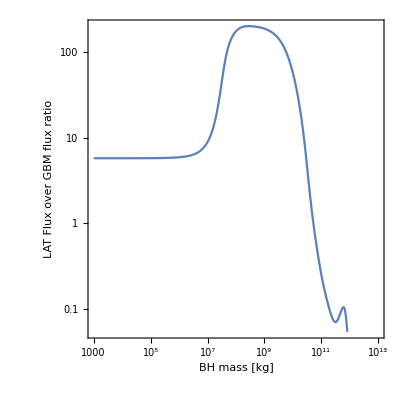

```mathematica
(* This is the LAT to GBM hardness ratio*)
LogLogPlot[PhotonFlux[MPBH,100 10^-3,100]/PhotonFlux[MPBH,30 10^-3,100 10^-3],{MPBH,10^3,10^13},Frame->True,FrameLabel->{ "BH mass [kg]","LAT Flux over GBM flux ratio"},LabelStyle->Directive[Bold],AspectRatio->1]
```

```mathematica
MPBH=10^6;
PhotonFlux[MPBH,100 10^-6,300 10^-6]/PhotonFlux[MPBH,50 10^-6,100 10^-6]

MPBH=10^6;
PhotonFlux[MPBH,100 10^-3,100]/PhotonFlux[MPBH,30 10^-3,100 10^-3]
```

1.58496

5.89222